```mathematica
Clear["Global`*"]
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]]
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]]
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3+ⅈ (y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3)

x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7+ⅈ (y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7)

```mathematica
L={};
For[i=38 30,i<384 3,i++;
μ=N[i/300,100];
For[j=1,j<10,j++;
x0=RandomReal[];
y0=RandomReal[] 10^-1;
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,x0},{y,y0}},];
L=Append[L,{μ,tab1⟦1,2⟧,tab1⟦2,2⟧}];
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,x0},{y,-y0}}];
L=Append[L,{μ,tab1⟦1,2⟧,tab1⟦2,2⟧}];
]
]
(*L = DeleteDuplicates[L];*)
Clear[μ]
```

FindRoot::fdssnv: Search specification Null without variables should be a list with 1 to 4 elements.

General::stop: Further output of FindRoot::fdssnv will be suppressed during this calculation.

```mathematica
ListPointPlot3D[L]
```

ListPointPlot3D::arrayerr: {«1»} must be a valid array or a list of valid arrays.

ListPointPlot3D[{{3.803333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333,Im[55.0165267037037037037037037037037037037037037037037037037037037037037037037037037037037037037037037 x-138 x^2+138 x^3-139 x^4+24+135 y^6-140 x y^6+140 x^2 y^6-11511.9985940846334685916780978509373571101966163694558756287151348879743941472336534064929126657522 y^8]+Re[1]==y,{y,0.0364143}},214,{1}}]
 |  |  |  |

-Graphics3D-

-Graphics3D-

```mathematica
Lnum = {}
For[i=0,i<Length[L],i++;
AppendTo[Lnum,L⟦i⟧];
AppendTo[Lnum⟦i⟧,i]]
```

{}

```mathematica
Lnum
```

{{3.80033,0.7368651872642595383279563961197266492706682749492008792330481108159545856141001919566587929210178059,1.857366524519838438030343962205182829593836956104322090781468222427479218619087077340626764109060458×10^-104,1},{3.80033,0.736865,-5.92656×10^-28,2},2157,{3.84,0.169434,-4.85199×10^-19,2160}}
 |  |  |  |

```mathematica
L⟦1,1⟧ - L⟦2,1⟧;
L;
```

```mathematica
realpts = Select[L,#⟦1⟧>3.8284 &];
imaginarypts = Select[L, #⟦1⟧<3.8284 &];


ListPointPlot3D[imaginarypts]
```

-Graphics3D-

```mathematica
groupA = Select[imaginarypts, #⟦2⟧<0.1 &];
groupBstep = Select[imaginarypts, #⟦2⟧>0.1 &];
groupB = Select[groupBstep, #⟦2⟧<0.2 &];
groupCstep = Select[imaginarypts, #⟦2⟧>0.4 &];
groupC= Select[groupCstep, #⟦2⟧<0.6 &];
groupDstep = Select[imaginarypts, #⟦2⟧>0.6 &];
groupD = Select[groupDstep, #⟦2⟧<0.8 &];
groupE = Select[imaginarypts, #⟦2⟧>0.8 &];

B1 = Select[groupB, #⟦3⟧>0 &];
B2 = Select[groupB, #⟦3⟧<0 &];
C1 = Select[groupC, #⟦3⟧>0 &];
C2 = Select[groupC, #⟦3⟧<0 &];
E1 = Select[groupE, #⟦3⟧>0 &];
E2 = Select[groupE, #⟦3⟧<0 &];


ListPointPlot3D[B1,PlotRange->{{3.8,3.81},Automatic,Automatic}]
```

-Graphics3D-

```mathematica
B1x⟦1,1⟧-B1x⟦2,1⟧;
B1x = Drop[B1,0,-1];
B1y = Drop[B1,0,{2}];
```

```mathematica
DeleteDuplicates[
```

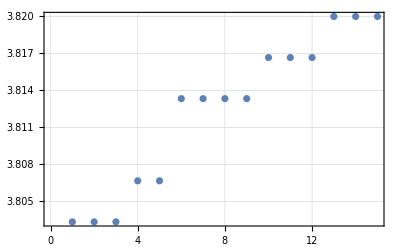

```mathematica
ListPlot[B1x⟦1;;15,1⟧,Frame->True,GridLines->Automatic]
```

```mathematica
ListPlot[B1y⟦1;;15,1⟧,Frame->True,GridLines->Automatic]
```

-Graphics-

```mathematica
B1x⟦1,1⟧ 10^18-B1x⟦2,1⟧10^18
```

0.

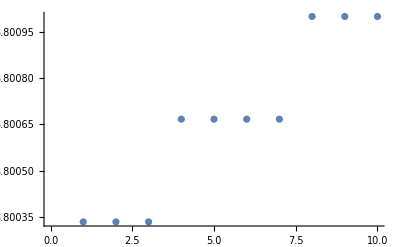

```mathematica
ListPlot[B1y⟦1;;10,1⟧]
```

```mathematica
ListPointPlot3D[realpts]
```

```mathematica
L
```

{{3.80033,0.514752,0.0409966},{3.80033,0.514752,-0.0409966},{3.80033,0.736865,-1.67084×10^-25},{3.80033,0.736865,1.29626×10^-25},{3.80033,0.955644,0.00459664},2150,{3.84,0.739583,1.60437×10^-22},{3.84,0.540388,3.25653×10^-17},{3.84,0.540388,-3.69483×10^-17},{3.84,0.739583,-2.78242×10^-22},{3.84,0.739583,1.25538×10^-22}}
 |  |  |  |

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

```mathematica
realpts;
```

```mathematica
imaginary = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7
```

x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7

```mathematica
real = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7
```

y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7

```mathematica
mat = {{D[real,x],D[real,y]},{D[imaginary,x],D[imaginary,y]}}
```

```mathematica
{{-2 y μ^3-2 y μ^4+12 x y μ^4-12 x^2 y μ^4+4 y^3 μ^4-2 y μ^5+12 x y μ^5-12 x^2 y μ^5+4 y^3 μ^5+12 x y μ^6-72 x^2 y μ^6+120 x^3 y μ^6-60 x^4 y μ^6+24 y^3 μ^6-120 x y^3 μ^6+120 x^2 y^3 μ^6-12 y^5 μ^6-12 x^2 y μ^7+80 x^3 y μ^7-180 x^4 y μ^7+168 x^5 y μ^7-56 x^6 y μ^7+4 y^3 μ^7-80 x y^3 μ^7+360 x^2 y^3 μ^7-560 x^3 y^3 μ^7+280 x^4 y^3 μ^7-36 y^5 μ^7+168 x y^5 μ^7-168 x^2 y^5 μ^7+8 y^7 μ^7,μ^3-2 x μ^3-2 x μ^4+6 x^2 μ^4-4 x^3 μ^4-6 y^2 μ^4+12 xe y^2 μ^4-2 x μ^5+6 x^2 μ^5-4 x^3 μ^5-6 y^2 μ^5+12 x y^2 μ^5+6 x^2 μ^6-24 x^3 μ^6+30 x^4 μ^6-12 x^5 μ^6-6 y^2 μ^6+72 x y^2 μ^6-180 x^2 y^2 μ^6+120 x^3 y^2 μ^6+30 y^4 μ^6-60 x y^4 μ^6-4 x^3 μ^7+20 x^4 μ^7-36 x^5 μ^7+28 x^6 μ^7-8 x^7 μ^7+12 x y^2 μ^7-120 x^2 y^2 μ^7+360 x^3 y^2 μ^7-420 x^4 y^2 μ^7+168 x^5 y^2 μ^7+20 y^4 μ^7-180 x y^4 μ^7+420 x^2 y^4 μ^7-280 x^3 y^4 μ^7-28 y^6 μ^7+56 x y^6 μ^7},{μ^3-2 x μ^3-2 x μ^4+6 x^2 μ^4-4 x^3 μ^4-6 y^2 μ^4+12 x y^2 μ^4-2 x μ^5+6 x^2 μ^5-4 x^3 μ^5-6 y^2 μ^5+12 x y^2 μ^5+6 x^2 μ^6-24 x^3 μ^6+30 x^4 μ^6-12 x^5 μ^6-6 y^2 μ^6+72 x y^2 μ^6-180 x^2 y^2 μ^6+120 x^3 y^2 μ^6+30 y^4 μ^6-60 x y^4 μ^6-4 x^3 μ^7+20 x^4 μ^7-36 x^5 μ^7+28 x^6 μ^7-8 x^7 μ^7+12 x y^2 μ^7-120 x^2 y^2 μ^7+360 x^3 y^2 μ^7-420 x^4 y^2 μ^7+168 x^5 y^2 μ^7+20 y^4 μ^7-180 x y^4 μ^7+420 x^2 y^4 μ^7-280 x^3 y^4 μ^7-28 y^6 μ^7+56 x y^6 μ^7,2 y μ^3+2 y μ^4-12 x y μ^4+12 x^2 y μ^4-4 y^3 μ^4+2 y μ^5-12 x y μ^5+12 x^2 y μ^5-4 y^3 μ^5-12 x y μ^6+72 x^2 y μ^6-120 x^3 y μ^6+60 x^4 y μ^6-24 y^3 μ^6+120 x y^3 μ^6-120 x^2 y^3 μ^6+12 y^5 μ^6+12 x^2 y μ^7-80 x^3 y μ^7+180 x^4 y μ^7-168 x^5 y μ^7+56 x^6 y μ^7-4 y^3 μ^7+80 x y^3 μ^7-360 x^2 y^3 μ^7+560 x^3 y^3 μ^7-280 x^4 y^3 μ^7+36 y^5 μ^7-168 x y^5 μ^7+168 x^2 y^5 μ^7-8 y^7 μ^7}}
```

```mathematica
L2 = DeleteDuplicates[Lnum]
```

{{3.80033,0.161172,0.0159191,1},{3.80033,0.161172,-0.0159191,2},{3.80033,0.161172,0.0159191,3},{3.80033,0.161172,-0.0159191,4},{3.80033,0.514752,0.0409966,5},2151,{3.84,0.149407,7.07596×10^-22,2157},{3.84,0.149407,-6.23648×10^-22,2158},{3.84,0.739583,2.5722×10^-18,2159},{3.84,0.739583,-3.52364×10^-18,2160}}
 |  |  |  |

```mathematica
Length[L2]
```

2160

```mathematica
Length[L]
```

2160

```mathematica
mat ={{-2 y μ^3-2 y μ^4+12 x y μ^4-12 x^2 y μ^4+4 y^3 μ^4-2 y μ^5+12 x y μ^5-12 x^2 y μ^5+4 y^3 μ^5+12 x y μ^6-72 x^2 y μ^6+120 x^3 y μ^6-60 x^4 y μ^6+24 y^3 μ^6-120 x y^3 μ^6+120 x^2 y^3 μ^6-12 y^5 μ^6-12 x^2 y μ^7+80 x^3 y μ^7-180 x^4 y μ^7+168 x^5 y μ^7-56 x^6 y μ^7+4 y^3 μ^7-80 x y^3 μ^7+360 x^2 y^3 μ^7-560 x^3 y^3 μ^7+280 x^4 y^3 μ^7-36 y^5 μ^7+168 x y^5 μ^7-168 x^2 y^5 μ^7+8 y^7 μ^7,μ^3-2 x μ^3-2 x μ^4+6 x^2 μ^4-4 x^3 μ^4-6 y^2 μ^4+12 x y^2 μ^4-2 x μ^5+6 x^2 μ^5-4 x^3 μ^5-6 y^2 μ^5+12 x y^2 μ^5+6 x^2 μ^6-24 x^3 μ^6+30 x^4 μ^6-12 x^5 μ^6-6 y^2 μ^6+72 x y^2 μ^6-180 x^2 y^2 μ^6+120 x^3 y^2 μ^6+30 y^4 μ^6-60 x y^4 μ^6-4 x^3 μ^7+20 x^4 μ^7-36 x^5 μ^7+28 x^6 μ^7-8 x^7 μ^7+12 x y^2 μ^7-120 x^2 y^2 μ^7+360 x^3 y^2 μ^7-420 x^4 y^2 μ^7+168 x^5 y^2 μ^7+20 y^4 μ^7-180 x y^4 μ^7+420 x^2 y^4 μ^7-280 x^3 y^4 μ^7-28 y^6 μ^7+56 x y^6 μ^7},{μ^3-2 x μ^3-2 x μ^4+6 x^2 μ^4-4 x^3 μ^4-6 y^2 μ^4+12 x y^2 μ^4-2 x μ^5+6 x^2 μ^5-4 x^3 μ^5-6 y^2 μ^5+12 x y^2 μ^5+6 x^2 μ^6-24 x^3 μ^6+30 x^4 μ^6-12 x^5 μ^6-6 y^2 μ^6+72 x y^2 μ^6-180 x^2 y^2 μ^6+120 x^3 y^2 μ^6+30 y^4 μ^6-60 x y^4 μ^6-4 x^3 μ^7+20 x^4 μ^7-36 x^5 μ^7+28 x^6 μ^7-8 x^7 μ^7+12 x y^2 μ^7-120 x^2 y^2 μ^7+360 x^3 y^2 μ^7-420 x^4 y^2 μ^7+168 x^5 y^2 μ^7+20 y^4 μ^7-180 x y^4 μ^7+420 x^2 y^4 μ^7-280 x^3 y^4 μ^7-28 y^6 μ^7+56 x y^6 μ^7,2 y μ^3+2 y μ^4-12 x y μ^4+12 x^2 y μ^4-4 y^3 μ^4+2 y μ^5-12 x y μ^5+12 x^2 y μ^5-4 y^3 μ^5-12 x y μ^6+72 x^2 y μ^6-120 x^3 y μ^6+60 x^4 y μ^6-24 y^3 μ^6+120 x y^3 μ^6-120 x^2 y^3 μ^6+12 y^5 μ^6+12 x^2 y μ^7-80 x^3 y μ^7+180 x^4 y μ^7-168 x^5 y μ^7+56 x^6 y μ^7-4 y^3 μ^7+80 x y^3 μ^7-360 x^2 y^3 μ^7+560 x^3 y^3 μ^7-280 x^4 y^3 μ^7+36 y^5 μ^7-168 x y^5 μ^7+168 x^2 y^5 μ^7-8 y^7 μ^7}}
```

{{-2 y μ^3-2 y μ^4+12 x y μ^4-12 x^2 y μ^4+4 y^3 μ^4-2 y μ^5+12 x y μ^5-12 x^2 y μ^5+4 y^3 μ^5+12 x y μ^6-72 x^2 y μ^6+120 x^3 y μ^6-60 x^4 y μ^6+24 y^3 μ^6-120 x y^3 μ^6+120 x^2 y^3 μ^6-12 y^5 μ^6-12 x^2 y μ^7+80 x^3 y μ^7-180 x^4 y μ^7+168 x^5 y μ^7-56 x^6 y μ^7+4 y^3 μ^7-80 x y^3 μ^7+360 x^2 y^3 μ^7-560 x^3 y^3 μ^7+280 x^4 y^3 μ^7-36 y^5 μ^7+168 x y^5 μ^7-168 x^2 y^5 μ^7+8 y^7 μ^7,μ^3-2 x μ^3-2 x μ^4+6 x^2 μ^4-4 x^3 μ^4-6 y^2 μ^4+12 x y^2 μ^4-2 x μ^5+6 x^2 μ^5-4 x^3 μ^5-6 y^2 μ^5+12 x y^2 μ^5+6 x^2 μ^6-24 x^3 μ^6+30 x^4 μ^6-12 x^5 μ^6-6 y^2 μ^6+72 x y^2 μ^6-180 x^2 y^2 μ^6+120 x^3 y^2 μ^6+30 y^4 μ^6-60 x y^4 μ^6-4 x^3 μ^7+20 x^4 μ^7-36 x^5 μ^7+28 x^6 μ^7-8 x^7 μ^7+12 x y^2 μ^7-120 x^2 y^2 μ^7+360 x^3 y^2 μ^7-420 x^4 y^2 μ^7+168 x^5 y^2 μ^7+20 y^4 μ^7-180 x y^4 μ^7+420 x^2 y^4 μ^7-280 x^3 y^4 μ^7-28 y^6 μ^7+56 x y^6 μ^7},{μ^3-2 x μ^3-2 x μ^4+6 x^2 μ^4-4 x^3 μ^4-6 y^2 μ^4+12 x y^2 μ^4-2 x μ^5+6 x^2 μ^5-4 x^3 μ^5-6 y^2 μ^5+12 x y^2 μ^5+6 x^2 μ^6-24 x^3 μ^6+30 x^4 μ^6-12 x^5 μ^6-6 y^2 μ^6+72 x y^2 μ^6-180 x^2 y^2 μ^6+120 x^3 y^2 μ^6+30 y^4 μ^6-60 x y^4 μ^6-4 x^3 μ^7+20 x^4 μ^7-36 x^5 μ^7+28 x^6 μ^7-8 x^7 μ^7+12 x y^2 μ^7-120 x^2 y^2 μ^7+360 x^3 y^2 μ^7-420 x^4 y^2 μ^7+168 x^5 y^2 μ^7+20 y^4 μ^7-180 x y^4 μ^7+420 x^2 y^4 μ^7-280 x^3 y^4 μ^7-28 y^6 μ^7+56 x y^6 μ^7,2 y μ^3+2 y μ^4-12 x y μ^4+12 x^2 y μ^4-4 y^3 μ^4+2 y μ^5-12 x y μ^5+12 x^2 y μ^5-4 y^3 μ^5-12 x y μ^6+72 x^2 y μ^6-120 x^3 y μ^6+60 x^4 y μ^6-24 y^3 μ^6+120 x y^3 μ^6-120 x^2 y^3 μ^6+12 y^5 μ^6+12 x^2 y μ^7-80 x^3 y μ^7+180 x^4 y μ^7-168 x^5 y μ^7+56 x^6 y μ^7-4 y^3 μ^7+80 x y^3 μ^7-360 x^2 y^3 μ^7+560 x^3 y^3 μ^7-280 x^4 y^3 μ^7+36 y^5 μ^7-168 x y^5 μ^7+168 x^2 y^5 μ^7-8 y^7 μ^7}}

```mathematica
autov = Eigenvalues[mat];
```

```mathematica
autov/.{y-> L⟦1,3⟧,x-> L⟦1,2⟧,μ-> L⟦1,1⟧}
```

{-2.95697,2.95697}

```mathematica
(*Lista de autovalores de todos os pontos fixos*)
autovlist = {}
For[i=0,i<Length[L2],i++;
autovlr = autov/.{μ-> L2⟦i,1⟧,x-> L2⟦i,2⟧,y-> L2⟦i,3⟧}; 
AppendTo[autovlist,{L2⟦i,1⟧,autovlr⟦1⟧,autovlr⟦2⟧}];
AppendTo[autovlist⟦i⟧,i]]
```

{}

```mathematica
autovlist
```

{{3.80033,-2.95697,2.95697,1},{3.80033,-2.95697,2.95697,2},{3.80033,-2.95697,2.95697,3},{3.80033,-2.95697,2.95697,4},{3.80033,-2.95697,2.95697,5},2150,{3.84,-2.74408,2.74408,2156},{3.84,-0.875277,0.875277,2157},{3.84,-0.875277,0.875277,2158},{3.84,-6.2295,6.2295,2159},{3.84,-6.2295,6.2295,2160}}
 |  |  |  |

```mathematica
step = Select[autovlist,#⟦3⟧<1&];
```

```mathematica
atrat = Select[step,#⟦3⟧>-1&];
```

```mathematica
atratpts = {}
For[i=0,i <Length[atrat],i++;
AppendTo[atratpts,Lnum⟦atrat⟦i,4⟧⟧]]
```

{}

```mathematica
atratpts
```

{{3.82867,0.956738,3.77084×10^-20,1537},{3.82867,0.956738,1.79439×10^-19,1538},{3.82867,0.510579,1.92164×10^-18,1539},{3.82867,0.510579,-4.39978×10^-18,1540},{3.82867,0.158469,3.05292×10^-16,1543},{3.82867,0.158469,-3.15605×10^-16,1544},{3.82867,0.510579,7.64188×10^-23,1545},{3.82867,0.510579,-1.48408×10^-22,1546},{3.82867,0.510579,2.74202×10^-18,1547},{3.82867,0.510579,-3.16365×10^-18,1548},{3.829,0.508513,2.63253×10^-20,1549},{3.829,0.508513,8.01595×10^-20,1550},{3.829,0.508513,9.49233×10^-22,1557},{3.829,0.508513,4.17266×10^-22,1558},{3.82933,0.507004,-2.45802×10^-15,1567},{3.82933,0.507004,-7.43273×10^-26,1568},{3.82933,0.507004,-2.47347×10^-14,1579},{3.82933,0.507004,3.12669×10^-14,1580},{3.82967,0.15658,-8.17355×10^-16,1585},{3.82967,0.15658,8.25929×10^-16,1586},{3.82967,0.15658,3.68581×10^-16,1589},{3.82967,0.15658,-3.6954×10^-16,1590},{3.82967,0.505756,3.55325×10^-18,1595},{3.82967,0.505756,-3.42889×10^-18,1596},{3.82967,0.505756,-6.51828×10^-22,1601},{3.82967,0.505756,1.09097×10^-21,1602},{3.83,0.156149,1.96546×10^-15,1613},{3.83,0.156149,-1.97907×10^-15,1614},{3.83033,0.503687,-3.10844×10^-22,1625},{3.83033,0.503687,-1.22182×10^-22,1626},{3.83033,0.503687,1.54925×10^-15,1627},{3.83033,0.503687,-1.27925×10^-15,1628},{3.83033,0.503687,-1.6979×10^-17,1635},{3.83033,0.503687,1.52906×10^-17,1636},{3.83067,0.50279,9.72334×10^-24,1639},{3.83067,0.50279,-9.71338×10^-24,1640},{3.83067,0.50279,7.44189×10^-25,1643},{3.83067,0.50279,2.32935×10^-24,1644},{3.83067,0.50279,1.09185×10^-13,1645},{3.83067,0.50279,-3.05388×10^-24,1646},{3.831,0.155073,1.59373×10^-23,1661},{3.831,0.155073,-9.64258×10^-24,1662},{3.831,0.501957,1.92488×10^-24,1671},{3.831,0.501957,-9.01132×10^-24,1672},{3.831,0.501957,-9.63491×10^-24,1673},{3.831,0.501957,4.20426×10^-23,1674},{3.83133,0.501177,2.56486×10^-22,1677},{3.83133,0.501177,-5.75944×10^-22,1678},{3.83133,0.501177,1.80513×10^-17,1679},{3.83133,0.501177,-1.83004×10^-17,1680},{3.83133,0.957828,8.31146×10^-19,1681},{3.83133,0.957828,3.19699×10^-16,1682},{3.83133,0.501177,-1.84166×10^-18,1685},{3.83133,0.501177,2.67844×10^-18,1686},{3.83133,0.957828,-1.21388×10^-16,1691},{3.83133,0.957828,-3.05058×10^-17,1692},{3.83167,0.154466,-8.74192×10^-21,1705},{3.83167,0.154466,1.03087×10^-20,1706},{3.83167,0.50044,-2.59417×10^-24,1707},{3.83167,0.50044,2.49494×10^-24,1708},{3.832,0.499739,-1.20133×10^-19,1723},{3.832,0.499739,-1.20373×10^-18,1724},{3.832,0.154185,1.95228×10^-15,1725},{3.832,0.154185,-1.95355×10^-15,1726},{3.832,0.958,-1.25582×10^-20,1727},{3.832,0.958,-2.2046×10^-12,1728},{3.83233,0.499071,1.47668×10^-25,1731},{3.83233,0.499071,2.66781×10^-24,1732},{3.83233,0.499071,-6.20762×10^-19,1733},{3.83233,0.499071,7.99374×10^-19,1734},{3.83233,0.499071,7.75151×10^-21,1737},{3.83233,0.499071,-1.32571×10^-20,1738},{3.83233,0.499071,1.71421×10^-13,1739},{3.83233,0.499071,4.9284×10^-24,1740},{3.83233,0.153917,1.04123×10^-20,1743},{3.83233,0.153917,-9.45684×10^-21,1744},{3.83233,0.499071,-5.73967×10^-21,1745},{3.83233,0.499071,-2.85277×10^-21,1746},{3.83267,0.498431,2.28764×10^-20,1749},{3.83267,0.498431,-2.14556×10^-20,1750},{3.83267,0.498431,1.48637×10^-21,1759},{3.83267,0.498431,6.34528×10^-22,1760},{3.83267,0.498431,2.45325×10^-15,1763},{3.83267,0.498431,-2.62612×10^-15,1764},{3.833,0.153411,1.30368×10^-18,1765},{3.833,0.153411,-1.35262×10^-18,1766},{3.833,0.497815,-1.39203×10^-24,1767},{3.833,0.497815,8.58701×10^-23,1768},{3.833,0.497815,-1.15366×10^-20,1773},{3.833,0.497815,1.00726×10^-20,1774},{3.833,0.153411,1.03866×10^-22,1779},{3.833,0.153411,-1.05816×10^-22,1780},{3.83333,0.153171,-1.12453×10^-24,1785},{3.83333,0.153171,4.89958×10^-25,1786},{3.83333,0.958304,3.04673×10^-22,1797},{3.83333,0.958304,-2.77541×10^-21,1798},{3.83367,0.152939,-7.00828×10^-16,1801},{3.83367,0.152939,7.09616×10^-16,1802},{3.83367,0.152939,-8.32848×10^-25,1803},{3.83367,0.152939,1.15684×10^-24,1804},{3.83367,0.496647,-6.6103×10^-23,1807},{3.83367,0.496647,-9.87183×10^-22,1808},{3.83367,0.152939,2.04226×10^-20,1809},{3.83367,0.152939,-1.88374×10^-20,1810},{3.83367,0.152939,-4.58654×10^-22,1815},{3.83367,0.152939,5.18426×10^-22,1816},{3.834,0.49609,-4.96988×10^-16,1819},{3.834,0.49609,5.02463×10^-16,1820},{3.834,0.49609,1.92707×10^-14,1829},{3.834,0.49609,1.25454×10^-25,1830},{3.834,0.49609,1.30013×10^-15,1831},{3.834,0.49609,-1.38579×10^-26,1832},{3.83433,0.49555,-2.66269×10^-25,1837},{3.83433,0.49555,3.32194×10^-14,1838},{3.83433,0.49555,1.35415×10^-20,1839},{3.83433,0.49555,-2.69158×10^-20,1840},{3.83433,0.49555,3.52624×10^-25,1841},{3.83433,0.49555,9.65104×10^-15,1842},{3.83433,0.152495,-1.8889×10^-21,1847},{3.83433,0.152495,1.80433×10^-21,1848},{3.83433,0.958507,2.14627×10^-16,1849},{3.83433,0.958507,-2.14034×10^-16,1850},{3.83433,0.152495,-3.42192×10^-15,1851},{3.83433,0.152495,3.86542×10^-27,1852},{3.83433,0.958507,1.03528×10^-21,1853},{3.83433,0.958507,-8.24949×10^-22,1854},{3.83467,0.152282,2.16136×10^-22,1859},{3.83467,0.152282,-1.70052×10^-22,1860},{3.83467,0.152282,2.62353×10^-20,1863},{3.83467,0.152282,-2.7886×10^-20,1864},{3.83467,0.152282,1.32669×10^-18,1865},{3.83467,0.152282,-1.38461×10^-18,1866},{3.83467,0.152282,-2.05658×10^-15,1871},{3.83467,0.152282,2.05708×10^-15,1872},{3.835,0.958635,5.98658×10^-19,1879},{3.835,0.958635,1.88706×10^-19,1880},{3.835,0.494514,1.18378×10^-18,1887},{3.835,0.494514,-1.1273×10^-18,1888},{3.83533,0.494016,-8.35265×10^-16,1891},{3.83533,0.494016,8.43811×10^-16,1892},{3.83533,0.151871,-1.23919×10^-17,1895},{3.83533,0.151871,1.23898×10^-17,1896},{3.83533,0.494016,3.45509×10^-21,1897},{3.83533,0.494016,-2.31987×10^-21,1898},{3.83533,0.151871,1.98793×10^-28,1905},{3.83533,0.151871,-4.51307×10^-27,1906},{3.83567,0.958756,2.439×10^-23,1911},{3.83567,0.958756,-1.99676×10^-23,1912},{3.83567,0.151673,3.22274×10^-19,1913},{3.83567,0.151673,-3.34461×10^-19,1914},{3.83567,0.493529,-4.94351×10^-19,1915},{3.83567,0.493529,5.49089×10^-19,1916},{3.83567,0.493529,-2.50384×10^-17,1919},{3.83567,0.493529,4.05515×10^-17,1920},{3.836,0.493054,-3.13557×10^-23,1931},{3.836,0.493054,1.83499×10^-22,1932},{3.836,0.151479,4.23454×10^-20,1935},{3.836,0.151479,-3.3018×10^-20,1936},{3.836,0.151479,-2.47722×10^-18,1937},{3.836,0.151479,2.41869×10^-18,1938},{3.83633,0.151289,7.59596×10^-19,1945},{3.83633,0.151289,-7.16091×10^-19,1946},{3.83633,0.492589,1.3209×10^-25,1949},{3.83633,0.492589,7.19788×10^-26,1950},{3.83633,0.151289,-1.42613×10^-25,1955},{3.83633,0.151289,1.0986×10^-25,1956},{3.83633,0.492589,1.73621×10^-21,1957},{3.83633,0.492589,-2.11918×10^-22,1958},{3.83633,0.151289,-9.30755×10^-16,1959},{3.83633,0.151289,9.27766×10^-16,1960},{3.83633,0.151289,6.25974×10^-24,1961},{3.83633,0.151289,-1.02418×10^-23,1962},{3.83667,0.492133,5.79611×10^-23,1965},{3.83667,0.492133,-1.1666×10^-23,1966},{3.83667,0.151103,8.63517×10^-22,1969},{3.83667,0.151103,-1.13675×10^-21,1970},{3.83667,0.151103,5.36173×10^-26,1975},{3.83667,0.151103,5.37688×10^-26,1976},{3.83667,0.492133,4.73596×10^-16,1977},{3.83667,0.492133,-4.29852×10^-16,1978},{3.83667,0.151103,-3.76491×10^-21,1979},{3.83667,0.151103,3.74488×10^-21,1980},{3.837,0.491687,2.98851×10^-24,1981},{3.837,0.491687,-3.66158×10^-24,1982},{3.837,0.491687,-1.14976×10^-21,1987},{3.837,0.491687,2.74315×10^-21,1988},{3.837,0.15092,5.3295×10^-16,1995},{3.837,0.15092,-5.37274×10^-16,1996},{3.837,0.958985,-2.7627×10^-15,1997},{3.837,0.958985,2.55709×10^-15,1998},{3.83733,0.150741,-3.56437×10^-22,1999},{3.83733,0.150741,3.23376×10^-22,2000},{3.83733,0.150741,1.02188×10^-22,2001},{3.83733,0.150741,-1.75974×10^-22,2002},{3.83733,0.959039,-4.78306×10^-19,2009},{3.83733,0.959039,2.53733×10^-18,2010},{3.83733,0.150741,-1.84573×10^-19,2011},{3.83733,0.150741,1.8704×10^-19,2012},{3.83767,0.150565,-5.41585×10^-24,2017},{3.83767,0.150565,1.76763×10^-23,2018},{3.83767,0.490819,-1.5497×10^-23,2021},{3.83767,0.490819,1.78728×10^-23,2022},{3.83767,0.150565,-3.79883×10^-15,2023},{3.83767,0.150565,3.80644×10^-15,2024},{3.83767,0.150565,2.17707×10^-22,2025},{3.83767,0.150565,-1.78858×10^-22,2026},{3.83767,0.959093,-1.01853×10^-18,2029},{3.83767,0.959093,-1.65512×10^-19,2030},{3.83767,0.490819,-1.48503×10^-28,2033},{3.83767,0.490819,6.17422×10^-27,2034},{3.838,0.150392,1.73936×10^-24,2045},{3.838,0.150392,-8.77466×10^-25,2046},{3.838,0.490397,-1.95795×10^-25,2047},{3.838,0.490397,-3.4441×10^-25,2048},{3.83833,0.489982,1.60302×10^-16,2053},{3.83833,0.489982,-1.58428×10^-16,2054},{3.83833,0.489982,-3.42379×10^-18,2059},{3.83833,0.489982,2.84117×10^-18,2060},{3.83867,0.489574,3.00291×10^-20,2073},{3.83867,0.489574,-6.02676×10^-21,2074},{3.83867,0.489574,2.61591×10^-16,2085},{3.83867,0.489574,-2.69538×10^-16,2086},{3.839,0.149888,1.00617×10^-17,2089},{3.839,0.149888,-1.01162×10^-17,2090},{3.839,0.489172,7.89638×10^-14,2099},{3.839,0.489172,-7.79458×10^-14,2100},{3.839,0.149888,3.32831×10^-21,2101},{3.839,0.149888,-3.53207×10^-21,2102},{3.83933,0.149726,7.5511×10^-15,2109},{3.83933,0.149726,-7.55854×10^-15,2110},{3.83933,0.488777,1.99652×10^-18,2113},{3.83933,0.488777,-2.79243×10^-18,2114},{3.83933,0.488777,1.61811×10^-25,2115},{3.83933,0.488777,2.03993×10^-25,2116},{3.83933,0.488777,5.69107×10^-20,2117},{3.83933,0.488777,-5.07916×10^-20,2118},{3.83967,0.149565,1.65599×10^-17,2129},{3.83967,0.149565,-1.84724×10^-17,2130},{3.83967,0.488388,-9.62251×10^-16,2131},{3.83967,0.488388,8.98794×10^-16,2132},{3.83967,0.488388,8.28082×10^-20,2135},{3.83967,0.488388,-1.19637×10^-19,2136},{3.83967,0.488388,8.09785×10^-27,2137},{3.83967,0.488388,-1.67173×10^-26,2138},{3.83967,0.149565,-2.06679×10^-24,2139},{3.83967,0.149565,1.18348×10^-24,2140},{3.84,0.959447,6.99525×10^-16,2145},{3.84,0.959447,-9.03316×10^-16,2146},{3.84,0.488004,-2.91991×10^-20,2151},{3.84,0.488004,2.95044×10^-20,2152},{3.84,0.149407,7.07596×10^-22,2157},{3.84,0.149407,-6.23648×10^-22,2158}}

```mathematica
atratdatax = Drop[atratpts,0,-2];
```

```mathematica
atratdataystep = Drop[atratpts,0,{2}];
atratdatay =Drop[atratdataystep,0,{3}];
```

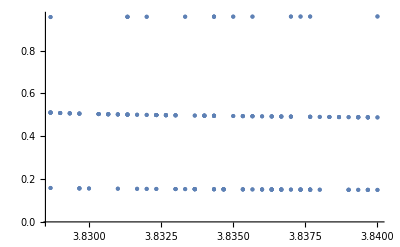

```mathematica
ListPlot[atratdatax]
```

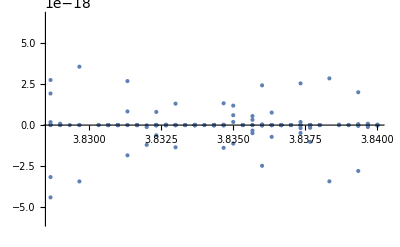

```mathematica
ListPlot[atratdatay]
```

```mathematica
datax = Drop[L,0,-1];
```

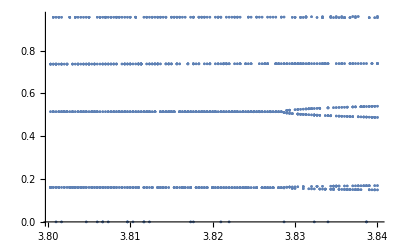

```mathematica
ListPlot[datax]
```

```mathematica
datay = Drop[L,0,{2}]
```

{{3.80033,0.0159191},{3.80033,-0.0159191},{3.80033,0.0159191},{3.80033,-0.0159191},{3.80033,0.0409966},{3.80033,-0.0409966},{3.80033,3.0932×10^-17},{3.80033,-4.0985×10^-17},2145,{3.84,-1.49643×10^-22},{3.84,-4.02522×10^-16},{3.84,3.99901×10^-16},{3.84,7.07596×10^-22},{3.84,-6.23648×10^-22},{3.84,2.5722×10^-18},{3.84,-3.52364×10^-18}}
 |  |  |  |

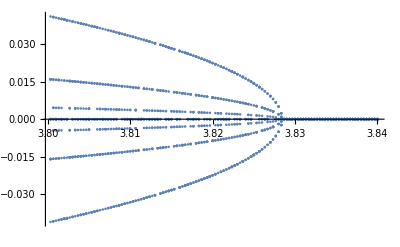

```mathematica
ListPlot[datay]
```

```mathematica
fx = Interpolation[datax]
```

Interpolation::inddp: The point 3.80033 in dimension 1 is duplicated.

Interpolation[{{3.80033,0.161172},{3.80033,0.161172},{3.80033,0.161172},{3.80033,0.161172},{3.80033,0.514752},{3.80033,0.514752},{3.80033,0.736865},{3.80033,0.736865},2144,{3.84,0.739583},{3.84,0.739583},{3.84,0.169434},{3.84,0.169434},{3.84,0.149407},{3.84,0.149407},{3.84,0.739583},{3.84,0.739583}}]
 |  |  |  |

```mathematica
ListPointPlot3D[L,PlotRange->Full]
```

-Graphics3D-

```mathematica
L;
```

```mathematica
Length[L]
```

2160

```mathematica
Length[datay]
```

2160

```mathematica
datay⟦1200⟧
```

{3.82233,-0.0190447}

```mathematica
{3.8400000000000003,-1.1102304573599482*^-18}
```

{3.84,-1.11023×10^-18}

```mathematica
datax⟦1200⟧
```

{3.82233,0.51444}

```mathematica
L⟦1200⟧
```

{3.82233,0.51444,-0.0190447}

```mathematica
Clear[L]
```

```mathematica
mat2 = {{12 y μ^4-24 x y μ^4+12 y μ^5-24 x y μ^5+12 y μ^6-144 x y μ^6+360 x^2 y μ^6-240 x^3 y μ^6-120 y^3 μ^6+240 x y^3 μ^6-24 x y μ^7+240 x^2 y μ^7-720 x^3 y μ^7+840 x^4 y μ^7-336 x^5 y μ^7-80 y^3 μ^7+720 x y^3 μ^7-1680 x^2 y^3 μ^7+1120 x^3 y^3 μ^7+168 y^5 μ^7-336 x y^5 μ^7,-12 y μ^4+24 x y μ^4-12 y μ^5+24 x y μ^5-12 y μ^6+144 x y μ^6-360 x^2 y μ^6+240 x^3 y μ^6+120 y^3 μ^6-240 x y^3 μ^6+24 x y μ^7-240 x^2 y μ^7+720 x^3 y μ^7-840 x^4 y μ^7+336 x^5 y μ^7+80 y^3 μ^7-720 x y^3 μ^7+1680 x^2 y^3 μ^7-1120 x^3 y^3 μ^7-168 y^5 μ^7+336 x y^5 μ^7},{-2 μ^3-2 μ^4+12 x μ^4-12 x^2 μ^4+12 y^2 μ^4-2 μ^5+12 x μ^5-12 x^2 μ^5+12 y^2 μ^5+12 x μ^6-72 x^2 μ^6+120 x^3 μ^6-60 x^4 μ^6+72 y^2 μ^6-360 x y^2 μ^6+360 x^2 y^2 μ^6-60 y^4 μ^6-12 x^2 μ^7+80 x^3 μ^7-180 x^4 μ^7+168 x^5 μ^7-56 x^6 μ^7+12 y^2 μ^7-240 x y^2 μ^7+1080 x^2 y^2 μ^7-1680 x^3 y^2 μ^7+840 x^4 y^2 μ^7-180 y^4 μ^7+840 x y^4 μ^7-840 x^2 y^4 μ^7+56 y^6 μ^7,2 μ^3+2 μ^4-12 x μ^4+12 x^2 μ^4-12 y^2 μ^4+2 μ^5-12 x μ^5+12 x^2 μ^5-12 y^2 μ^5-12 x μ^6+72 x^2 μ^6-120 x^3 μ^6+60 x^4 μ^6-72 y^2 μ^6+360 x y^2 μ^6-360 x^2 y^2 μ^6+60 y^4 μ^6+12 x^2 μ^7-80 x^3 μ^7+180 x^4 μ^7-168 x^5 μ^7+56 x^6 μ^7-12 y^2 μ^7+240 x y^2 μ^7-1080 x^2 y^2 μ^7+1680 x^3 y^2 μ^7-840 x^4 y^2 μ^7+180 y^4 μ^7-840 x y^4 μ^7+840 x^2 y^4 μ^7-56 y^6 μ^7}}
```

{{12 y μ^4-24 x y μ^4+12 y μ^5-24 x y μ^5+12 y μ^6-144 x y μ^6+360 x^2 y μ^6-240 x^3 y μ^6-120 y^3 μ^6+240 x y^3 μ^6-24 x y μ^7+240 x^2 y μ^7-720 x^3 y μ^7+840 x^4 y μ^7-336 x^5 y μ^7-80 y^3 μ^7+720 x y^3 μ^7-1680 x^2 y^3 μ^7+1120 x^3 y^3 μ^7+168 y^5 μ^7-336 x y^5 μ^7,-12 y μ^4+24 x y μ^4-12 y μ^5+24 x y μ^5-12 y μ^6+144 x y μ^6-360 x^2 y μ^6+240 x^3 y μ^6+120 y^3 μ^6-240 x y^3 μ^6+24 x y μ^7-240 x^2 y μ^7+720 x^3 y μ^7-840 x^4 y μ^7+336 x^5 y μ^7+80 y^3 μ^7-720 x y^3 μ^7+1680 x^2 y^3 μ^7-1120 x^3 y^3 μ^7-168 y^5 μ^7+336 x y^5 μ^7},{-2 μ^3-2 μ^4+12 x μ^4-12 x^2 μ^4+12 y^2 μ^4-2 μ^5+12 x μ^5-12 x^2 μ^5+12 y^2 μ^5+12 x μ^6-72 x^2 μ^6+120 x^3 μ^6-60 x^4 μ^6+72 y^2 μ^6-360 x y^2 μ^6+360 x^2 y^2 μ^6-60 y^4 μ^6-12 x^2 μ^7+80 x^3 μ^7-180 x^4 μ^7+168 x^5 μ^7-56 x^6 μ^7+12 y^2 μ^7-240 x y^2 μ^7+1080 x^2 y^2 μ^7-1680 x^3 y^2 μ^7+840 x^4 y^2 μ^7-180 y^4 μ^7+840 x y^4 μ^7-840 x^2 y^4 μ^7+56 y^6 μ^7,2 μ^3+2 μ^4-12 x μ^4+12 x^2 μ^4-12 y^2 μ^4+2 μ^5-12 x μ^5+12 x^2 μ^5-12 y^2 μ^5-12 x μ^6+72 x^2 μ^6-120 x^3 μ^6+60 x^4 μ^6-72 y^2 μ^6+360 x y^2 μ^6-360 x^2 y^2 μ^6+60 y^4 μ^6+12 x^2 μ^7-80 x^3 μ^7+180 x^4 μ^7-168 x^5 μ^7+56 x^6 μ^7-12 y^2 μ^7+240 x y^2 μ^7-1080 x^2 y^2 μ^7+1680 x^3 y^2 μ^7-840 x^4 y^2 μ^7+180 y^4 μ^7-840 x y^4 μ^7+840 x^2 y^4 μ^7-56 y^6 μ^7}}

```mathematica
autov2 =Eigenvalues[mat2]
```

{0,2 μ^3 (1+μ-6 x μ+6 x^2 μ+6 y μ-12 x y μ-6 y^2 μ+μ^2-6 x μ^2+6 x^2 μ^2+6 y μ^2-12 x y μ^2-6 y^2 μ^2-6 x μ^3+36 x^2 μ^3-60 x^3 μ^3+30 x^4 μ^3+6 y μ^3-72 x y μ^3+180 x^2 y μ^3-120 x^3 y μ^3-36 y^2 μ^3+180 x y^2 μ^3-180 x^2 y^2 μ^3-60 y^3 μ^3+120 x y^3 μ^3+30 y^4 μ^3+6 x^2 μ^4-40 x^3 μ^4+90 x^4 μ^4-84 x^5 μ^4+28 x^6 μ^4-12 x y μ^4+120 x^2 y μ^4-360 x^3 y μ^4+420 x^4 y μ^4-168 x^5 y μ^4-6 y^2 μ^4+120 x y^2 μ^4-540 x^2 y^2 μ^4+840 x^3 y^2 μ^4-420 x^4 y^2 μ^4-40 y^3 μ^4+360 x y^3 μ^4-840 x^2 y^3 μ^4+560 x^3 y^3 μ^4+90 y^4 μ^4-420 x y^4 μ^4+420 x^2 y^4 μ^4+84 y^5 μ^4-168 x y^5 μ^4-28 y^6 μ^4)}

```mathematica
autovlist2 = {}
For[i=0,i<Length[atratpts],i++;
autovlr2 = autov2/.{μ-> atratpts⟦i,1⟧,x-> atratpts⟦i,2⟧,y-> atratpts⟦i,3⟧}; 
AppendTo[autovlist2,{atratpts⟦i,1⟧,autovlr2⟦1⟧,autovlr2⟦2⟧}];
AppendTo[autovlist2⟦i⟧,atratpts⟦i,4⟧]]
```

{}

```mathematica
autovlist2
```

{{3.82867,0,631.383,1537},{3.82867,0,631.383,1538},{3.82867,0,-69.2913,1539},{3.82867,0,-69.2913,1540},{3.82867,0,-180.65,1543},{3.82867,0,-180.65,1544},{3.82867,0,-69.2913,1545},{3.82867,0,-69.2913,1546},{3.82867,0,-69.2913,1547},{3.82867,0,-69.2913,1548},{3.829,0,-69.7731,1549},{3.829,0,-69.7731,1550},{3.829,0,-69.7731,1557},{3.829,0,-69.7731,1558},{3.82933,0,-70.0954,1567},{3.82933,0,-70.0954,1568},{3.82933,0,-70.0954,1579},{3.82933,0,-70.0954,1580},{3.82967,0,-184.327,1585},{3.82967,0,-184.327,1586},{3.82967,0,-184.327,1589},{3.82967,0,-184.327,1590},{3.82967,0,-70.3433,1595},{3.82967,0,-70.3433,1596},{3.82967,0,-70.3433,1601},{3.82967,0,-70.3433,1602},{3.83,0,-185.167,1613},{3.83,0,-185.167,1614},{3.83033,0,-70.7165,1625},{3.83033,0,-70.7165,1626},{3.83033,0,-70.7165,1627},{3.83033,0,-70.7165,1628},{3.83033,0,-70.7165,1635},{3.83033,0,-70.7165,1636},{3.83067,0,-70.8636,1639},{3.83067,0,-70.8636,1640},{3.83067,0,-70.8636,1643},{3.83067,0,-70.8636,1644},{3.83067,0,-70.8636,1645},{3.83067,0,-70.8636,1646},{3.831,0,-187.274,1661},{3.831,0,-187.274,1662},{3.831,0,-70.9923,1671},{3.831,0,-70.9923,1672},{3.831,0,-70.9923,1673},{3.831,0,-70.9923,1674},{3.83133,0,-71.1058,1677},{3.83133,0,-71.1058,1678},{3.83133,0,-71.1058,1679},{3.83133,0,-71.1058,1680},{3.83133,0,658.967,1681},{3.83133,0,658.967,1682},{3.83133,0,-71.1058,1685},{3.83133,0,-71.1058,1686},{3.83133,0,658.967,1691},{3.83133,0,658.967,1692},{3.83167,0,-188.464,1705},{3.83167,0,-188.464,1706},{3.83167,0,-71.2068,1707},{3.83167,0,-71.2068,1708},{3.832,0,-71.2972,1723},{3.832,0,-71.2972,1724},{3.832,0,-189.015,1725},{3.832,0,-189.015,1726},{3.832,0,663.506,1727},{3.832,0,663.506,1728},{3.83233,0,-71.3783,1731},{3.83233,0,-71.3783,1732},{3.83233,0,-71.3783,1733},{3.83233,0,-71.3783,1734},{3.83233,0,-71.3783,1737},{3.83233,0,-71.3783,1738},{3.83233,0,-71.3783,1739},{3.83233,0,-71.3783,1740},{3.83233,0,-189.543,1743},{3.83233,0,-189.543,1744},{3.83233,0,-71.3783,1745},{3.83233,0,-71.3783,1746},{3.83267,0,-71.4513,1749},{3.83267,0,-71.4513,1750},{3.83267,0,-71.4513,1759},{3.83267,0,-71.4513,1760},{3.83267,0,-71.4513,1763},{3.83267,0,-71.4513,1764},{3.833,0,-190.539,1765},{3.833,0,-190.539,1766},{3.833,0,-71.5172,1767},{3.833,0,-71.5172,1768},{3.833,0,-71.5172,1773},{3.833,0,-71.5172,1774},{3.833,0,-190.539,1779},{3.833,0,-190.539,1780},{3.83333,0,-191.012,1785},{3.83333,0,-191.012,1786},{3.83333,0,671.673,1797},{3.83333,0,671.673,1798},{3.83367,0,-191.47,1801},{3.83367,0,-191.47,1802},{3.83367,0,-191.47,1803},{3.83367,0,-191.47,1804},{3.83367,0,-71.6304,1807},{3.83367,0,-71.6304,1808},{3.83367,0,-191.47,1809},{3.83367,0,-191.47,1810},{3.83367,0,-191.47,1815},{3.83367,0,-191.47,1816},{3.834,0,-71.6788,1819},{3.834,0,-71.6788,1820},{3.834,0,-71.6788,1829},{3.834,0,-71.6788,1830},{3.834,0,-71.6788,1831},{3.834,0,-71.6788,1832},{3.83433,0,-71.7225,1837},{3.83433,0,-71.7225,1838},{3.83433,0,-71.7225,1839},{3.83433,0,-71.7225,1840},{3.83433,0,-71.7225,1841},{3.83433,0,-71.7225,1842},{3.83433,0,-192.347,1847},{3.83433,0,-192.347,1848},{3.83433,0,677.241,1849},{3.83433,0,677.241,1850},{3.83433,0,-192.347,1851},{3.83433,0,-192.347,1852},{3.83433,0,677.241,1853},{3.83433,0,677.241,1854},{3.83467,0,-192.769,1859},{3.83467,0,-192.769,1860},{3.83467,0,-192.769,1863},{3.83467,0,-192.769,1864},{3.83467,0,-192.769,1865},{3.83467,0,-192.769,1866},{3.83467,0,-192.769,1871},{3.83467,0,-192.769,1872},{3.835,0,680.756,1879},{3.835,0,680.756,1880},{3.835,0,-71.7969,1887},{3.835,0,-71.7969,1888},{3.83533,0,-71.8283,1891},{3.83533,0,-71.8283,1892},{3.83533,0,-193.582,1895},{3.83533,0,-193.582,1896},{3.83533,0,-71.8283,1897},{3.83533,0,-71.8283,1898},{3.83533,0,-193.582,1905},{3.83533,0,-193.582,1906},{3.83567,0,684.143,1911},{3.83567,0,684.143,1912},{3.83567,0,-193.975,1913},{3.83567,0,-193.975,1914},{3.83567,0,-71.8562,1915},{3.83567,0,-71.8562,1916},{3.83567,0,-71.8562,1919},{3.83567,0,-71.8562,1920},{3.836,0,-71.8809,1931},{3.836,0,-71.8809,1932},{3.836,0,-194.36,1935},{3.836,0,-194.36,1936},{3.836,0,-194.36,1937},{3.836,0,-194.36,1938},{3.83633,0,-194.737,1945},{3.83633,0,-194.737,1946},{3.83633,0,-71.9024,1949},{3.83633,0,-71.9024,1950},{3.83633,0,-194.737,1955},{3.83633,0,-194.737,1956},{3.83633,0,-71.9024,1957},{3.83633,0,-71.9024,1958},{3.83633,0,-194.737,1959},{3.83633,0,-194.737,1960},{3.83633,0,-194.737,1961},{3.83633,0,-194.737,1962},{3.83667,0,-71.9211,1965},{3.83667,0,-71.9211,1966},{3.83667,0,-195.107,1969},{3.83667,0,-195.107,1970},{3.83667,0,-195.107,1975},{3.83667,0,-195.107,1976},{3.83667,0,-71.9211,1977},{3.83667,0,-71.9211,1978},{3.83667,0,-195.107,1979},{3.83667,0,-195.107,1980},{3.837,0,-71.9371,1981},{3.837,0,-71.9371,1982},{3.837,0,-71.9371,1987},{3.837,0,-71.9371,1988},{3.837,0,-195.47,1995},{3.837,0,-195.47,1996},{3.837,0,690.596,1997},{3.837,0,690.596,1998},{3.83733,0,-195.827,1999},{3.83733,0,-195.827,2000},{3.83733,0,-195.827,2001},{3.83733,0,-195.827,2002},{3.83733,0,692.152,2009},{3.83733,0,692.152,2010},{3.83733,0,-195.827,2011},{3.83733,0,-195.827,2012},{3.83767,0,-196.178,2017},{3.83767,0,-196.178,2018},{3.83767,0,-71.9615,2021},{3.83767,0,-71.9615,2022},{3.83767,0,-196.178,2023},{3.83767,0,-196.178,2024},{3.83767,0,-196.178,2025},{3.83767,0,-196.178,2026},{3.83767,0,693.687,2029},{3.83767,0,693.687,2030},{3.83767,0,-71.9615,2033},{3.83767,0,-71.9615,2034},{3.838,0,-196.523,2045},{3.838,0,-196.523,2046},{3.838,0,-71.9701,2047},{3.838,0,-71.9701,2048},{3.83833,0,-71.9766,2053},{3.83833,0,-71.9766,2054},{3.83833,0,-71.9766,2059},{3.83833,0,-71.9766,2060},{3.83867,0,-71.9809,2073},{3.83867,0,-71.9809,2074},{3.83867,0,-71.9809,2085},{3.83867,0,-71.9809,2086},{3.839,0,-197.528,2089},{3.839,0,-197.528,2090},{3.839,0,-71.9833,2099},{3.839,0,-71.9833,2100},{3.839,0,-197.528,2101},{3.839,0,-197.528,2102},{3.83933,0,-197.853,2109},{3.83933,0,-197.853,2110},{3.83933,0,-71.9838,2113},{3.83933,0,-71.9838,2114},{3.83933,0,-71.9838,2115},{3.83933,0,-71.9838,2116},{3.83933,0,-71.9838,2117},{3.83933,0,-71.9838,2118},{3.83967,0,-198.173,2129},{3.83967,0,-198.173,2130},{3.83967,0,-71.9824,2131},{3.83967,0,-71.9824,2132},{3.83967,0,-71.9824,2135},{3.83967,0,-71.9824,2136},{3.83967,0,-71.9824,2137},{3.83967,0,-71.9824,2138},{3.83967,0,-198.173,2139},{3.83967,0,-198.173,2140},{3.84,0,703.956,2145},{3.84,0,703.956,2146},{3.84,0,-71.9793,2151},{3.84,0,-71.9793,2152},{3.84,0,-198.49,2157},{3.84,0,-198.49,2158}}

```mathematica
step2 = Select[autovlist2,#⟦3⟧<1&];
atrat2 = Select[step2,#⟦3⟧>-1&]
```

{}

```mathematica
atratdatay2step = Drop[autovlist2,0,{2}];
atratdatay2 =Drop[atratdatay2step,0,{3}];
```

```mathematica
atratdatay2
```

{{3.82867,631.383},{3.82867,631.383},{3.82867,-69.2913},{3.82867,-69.2913},{3.82867,-180.65},{3.82867,-180.65},{3.82867,-69.2913},{3.82867,-69.2913},{3.82867,-69.2913},{3.82867,-69.2913},{3.829,-69.7731},{3.829,-69.7731},{3.829,-69.7731},{3.829,-69.7731},{3.82933,-70.0954},{3.82933,-70.0954},{3.82933,-70.0954},{3.82933,-70.0954},{3.82967,-184.327},{3.82967,-184.327},{3.82967,-184.327},{3.82967,-184.327},{3.82967,-70.3433},{3.82967,-70.3433},{3.82967,-70.3433},{3.82967,-70.3433},{3.83,-185.167},{3.83,-185.167},{3.83033,-70.7165},{3.83033,-70.7165},{3.83033,-70.7165},{3.83033,-70.7165},{3.83033,-70.7165},{3.83033,-70.7165},{3.83067,-70.8636},{3.83067,-70.8636},{3.83067,-70.8636},{3.83067,-70.8636},{3.83067,-70.8636},{3.83067,-70.8636},{3.831,-187.274},{3.831,-187.274},{3.831,-70.9923},{3.831,-70.9923},{3.831,-70.9923},{3.831,-70.9923},{3.83133,-71.1058},{3.83133,-71.1058},{3.83133,-71.1058},{3.83133,-71.1058},{3.83133,658.967},{3.83133,658.967},{3.83133,-71.1058},{3.83133,-71.1058},{3.83133,658.967},{3.83133,658.967},{3.83167,-188.464},{3.83167,-188.464},{3.83167,-71.2068},{3.83167,-71.2068},{3.832,-71.2972},{3.832,-71.2972},{3.832,-189.015},{3.832,-189.015},{3.832,663.506},{3.832,663.506},{3.83233,-71.3783},{3.83233,-71.3783},{3.83233,-71.3783},{3.83233,-71.3783},{3.83233,-71.3783},{3.83233,-71.3783},{3.83233,-71.3783},{3.83233,-71.3783},{3.83233,-189.543},{3.83233,-189.543},{3.83233,-71.3783},{3.83233,-71.3783},{3.83267,-71.4513},{3.83267,-71.4513},{3.83267,-71.4513},{3.83267,-71.4513},{3.83267,-71.4513},{3.83267,-71.4513},{3.833,-190.539},{3.833,-190.539},{3.833,-71.5172},{3.833,-71.5172},{3.833,-71.5172},{3.833,-71.5172},{3.833,-190.539},{3.833,-190.539},{3.83333,-191.012},{3.83333,-191.012},{3.83333,671.673},{3.83333,671.673},{3.83367,-191.47},{3.83367,-191.47},{3.83367,-191.47},{3.83367,-191.47},{3.83367,-71.6304},{3.83367,-71.6304},{3.83367,-191.47},{3.83367,-191.47},{3.83367,-191.47},{3.83367,-191.47},{3.834,-71.6788},{3.834,-71.6788},{3.834,-71.6788},{3.834,-71.6788},{3.834,-71.6788},{3.834,-71.6788},{3.83433,-71.7225},{3.83433,-71.7225},{3.83433,-71.7225},{3.83433,-71.7225},{3.83433,-71.7225},{3.83433,-71.7225},{3.83433,-192.347},{3.83433,-192.347},{3.83433,677.241},{3.83433,677.241},{3.83433,-192.347},{3.83433,-192.347},{3.83433,677.241},{3.83433,677.241},{3.83467,-192.769},{3.83467,-192.769},{3.83467,-192.769},{3.83467,-192.769},{3.83467,-192.769},{3.83467,-192.769},{3.83467,-192.769},{3.83467,-192.769},{3.835,680.756},{3.835,680.756},{3.835,-71.7969},{3.835,-71.7969},{3.83533,-71.8283},{3.83533,-71.8283},{3.83533,-193.582},{3.83533,-193.582},{3.83533,-71.8283},{3.83533,-71.8283},{3.83533,-193.582},{3.83533,-193.582},{3.83567,684.143},{3.83567,684.143},{3.83567,-193.975},{3.83567,-193.975},{3.83567,-71.8562},{3.83567,-71.8562},{3.83567,-71.8562},{3.83567,-71.8562},{3.836,-71.8809},{3.836,-71.8809},{3.836,-194.36},{3.836,-194.36},{3.836,-194.36},{3.836,-194.36},{3.83633,-194.737},{3.83633,-194.737},{3.83633,-71.9024},{3.83633,-71.9024},{3.83633,-194.737},{3.83633,-194.737},{3.83633,-71.9024},{3.83633,-71.9024},{3.83633,-194.737},{3.83633,-194.737},{3.83633,-194.737},{3.83633,-194.737},{3.83667,-71.9211},{3.83667,-71.9211},{3.83667,-195.107},{3.83667,-195.107},{3.83667,-195.107},{3.83667,-195.107},{3.83667,-71.9211},{3.83667,-71.9211},{3.83667,-195.107},{3.83667,-195.107},{3.837,-71.9371},{3.837,-71.9371},{3.837,-71.9371},{3.837,-71.9371},{3.837,-195.47},{3.837,-195.47},{3.837,690.596},{3.837,690.596},{3.83733,-195.827},{3.83733,-195.827},{3.83733,-195.827},{3.83733,-195.827},{3.83733,692.152},{3.83733,692.152},{3.83733,-195.827},{3.83733,-195.827},{3.83767,-196.178},{3.83767,-196.178},{3.83767,-71.9615},{3.83767,-71.9615},{3.83767,-196.178},{3.83767,-196.178},{3.83767,-196.178},{3.83767,-196.178},{3.83767,693.687},{3.83767,693.687},{3.83767,-71.9615},{3.83767,-71.9615},{3.838,-196.523},{3.838,-196.523},{3.838,-71.9701},{3.838,-71.9701},{3.83833,-71.9766},{3.83833,-71.9766},{3.83833,-71.9766},{3.83833,-71.9766},{3.83867,-71.9809},{3.83867,-71.9809},{3.83867,-71.9809},{3.83867,-71.9809},{3.839,-197.528},{3.839,-197.528},{3.839,-71.9833},{3.839,-71.9833},{3.839,-197.528},{3.839,-197.528},{3.83933,-197.853},{3.83933,-197.853},{3.83933,-71.9838},{3.83933,-71.9838},{3.83933,-71.9838},{3.83933,-71.9838},{3.83933,-71.9838},{3.83933,-71.9838},{3.83967,-198.173},{3.83967,-198.173},{3.83967,-71.9824},{3.83967,-71.9824},{3.83967,-71.9824},{3.83967,-71.9824},{3.83967,-71.9824},{3.83967,-71.9824},{3.83967,-198.173},{3.83967,-198.173},{3.84,703.956},{3.84,703.956},{3.84,-71.9793},{3.84,-71.9793},{3.84,-198.49},{3.84,-198.49}}

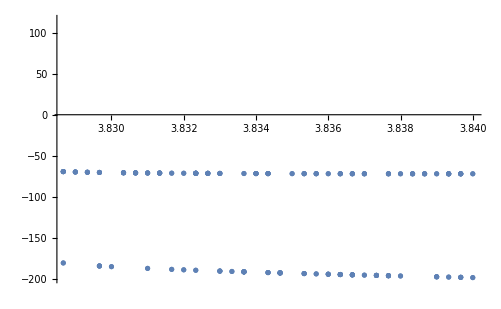

```mathematica
ListPlot[atratdatay2]
```

```mathematica
(*ou*)
Table[{L[[i,1]],L[[i,3]]},{i,3,Length[l]}]
```

{}

```mathematica
unstable = Select[autovlist,Abs[#⟦3⟧]>1&];
```

```mathematica
unstablepts = {}
For[i=0,i <Length[unstable],i++;
AppendTo[unstablepts,Lnum⟦unstable⟦i,4⟧⟧]]
```

{}

```mathematica
unstablepts
```

{{3.80033,0.161172,0.0159191,1},{3.80033,0.161172,-0.0159191,2},{3.80033,0.161172,0.0159191,3},{3.80033,0.161172,-0.0159191,4},{3.80033,0.514752,0.0409966,5},1899,{3.84,0.169434,-4.02522×10^-16,2155},{3.84,0.169434,3.99901×10^-16,2156},{3.84,0.739583,2.5722×10^-18,2159},{3.84,0.739583,-3.52364×10^-18,2160}}
 |  |  |  |

```mathematica
ListPointPlot3D[Drop[unstablepts,0,{4}]]
```

-Graphics3D-

```mathematica
autovlist2unstable = {}
For[i=0,i<Length[unstablepts],i++;
autovlr2 = autov2/.{μ->unstablepts⟦i,1⟧,x-> unstablepts⟦i,2⟧,y-> unstablepts⟦i,3⟧}; 
AppendTo[autovlist2unstable,{unstablepts⟦i,1⟧,autovlr2⟦1⟧,autovlr2⟦2⟧}];
AppendTo[autovlist2unstable⟦i⟧,unstablepts⟦i,4⟧]]
```

{}

```mathematica
autovlist2unstable
```

{{3.80033,0,-205.163,1},{3.80033,0,-144.665,2},{3.80033,0,-205.163,3},{3.80033,0,-144.665,4},{3.80033,0,-88.762,5},{3.80033,0,-65.0842,6},{3.80033,0,60.1314,7},{3.80033,0,60.1314,8},{3.80033,0,60.1314,9},{3.80033,0,60.1314,10},{3.80033,0,-144.665,11},{3.80033,0,-205.163,12},{3.80033,0,60.1314,13},{3.80033,0,60.1314,14},{3.80033,0,-205.163,15},1878,{3.83967,0,-159.679,2134},{3.83967,0,566.726,2141},{3.83967,0,566.726,2142},{3.84,0,-57.0947,2143},{3.84,0,-57.0947,2144},{3.84,0,566.102,2147},{3.84,0,566.102,2148},{3.84,0,66.1892,2149},{3.84,0,66.1892,2150},{3.84,0,66.1892,2153},{3.84,0,66.1892,2154},{3.84,0,-159.427,2155},{3.84,0,-159.427,2156},{3.84,0,66.1892,2159},{3.84,0,66.1892,2160}}
 |  |  |  |

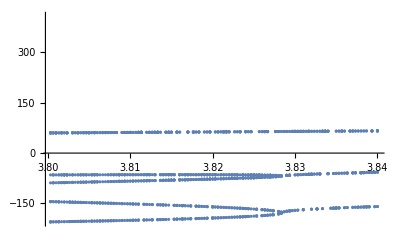

```mathematica
ListPlot[Table[{autovlist2unstable[[i,1]],autovlist2unstable[[i,3]]},{i,3,Length[autovlist2unstable]}]]
```

```mathematica
autovlistgroup = {}
For[i=0,i<Length[E1],i++;
autovlr = autov/.{μ-> E1⟦i,1⟧,x-> E1⟦i,2⟧,y-> E1⟦i,3⟧}; 
AppendTo[autovlistgroup,{E1⟦i,1⟧,autovlr⟦1⟧,autovlr⟦2⟧}];
AppendTo[autovlistgroup⟦i⟧,E1⟦i,4⟧]]

autovlistgroup
```

{}

{{3.80067,-2.94211,2.94211,22},{3.80067,-2.94211,2.94211,28},{3.801,-2.92713,2.92713,49},{3.80133,-2.91208,2.91208,55},{3.80133,-2.91207,2.91207,65},{3.80167,-2.89692,2.89692,89},{3.80267,-2.85087,2.85087,127},{3.80267,-2.85089,2.85089,138},{3.80267,-2.85089,2.85089,141},{3.80333,-2.81969,2.81969,163},{3.80333,-2.81967,2.81967,169},{3.80333,-2.81968,2.81968,171},{3.80367,-2.80392,2.80392,193},{3.804,-2.78806,2.78806,203},{3.80433,-2.7721,2.7721,228},{3.80467,-2.75601,2.75601,238},{3.805,-2.73981,2.73981,253},{3.805,-2.73981,2.73981,259},{3.805,-2.73981,2.73981,268},{3.806,-2.69054,2.69054,309},{3.80633,-2.67388,2.67388,331},{3.80633,-2.67387,2.67387,335},{3.80633,-2.67387,2.67387,338},{3.80667,-2.65709,2.65709,353},{3.807,-2.64019,2.64019,367},{3.807,-2.64016,2.64016,370},{3.807,-2.64017,2.64017,371},{3.807,-2.64017,2.64017,373},{3.80733,-2.62314,2.62314,389},{3.80767,-2.60596,2.60596,399},{3.80767,-2.60596,2.60596,401},{3.808,-2.58865,2.58865,428},{3.80833,-2.57121,2.57121,437},{3.80833,-2.5712,2.5712,441},{3.80833,-2.57122,2.57122,445},{3.80867,-2.55363,2.55363,458},{3.80867,-2.55363,2.55363,467},{3.809,-2.5359,2.5359,473},{3.80933,-2.51805,2.51805,489},{3.80967,-2.50003,2.50003,522},{3.81,-2.48187,2.48187,527},{3.81,-2.48187,2.48187,537},{3.81067,-2.44507,2.44507,565},{3.81067,-2.44507,2.44507,567},{3.81067,-2.44508,2.44508,569},{3.81067,-2.44507,2.44507,575},{3.81167,-2.38866,2.38866,613},{3.812,-2.36953,2.36953,633},{3.812,-2.36952,2.36952,647},{3.81233,-2.35021,2.35021,665},{3.81267,-2.3307,2.3307,671},{3.81267,-2.3307,2.3307,680},{3.813,-2.31101,2.31101,693},{3.81333,-2.29112,2.29112,713},{3.81333,-2.29113,2.29113,719},{3.81367,-2.27108,2.27108,725},{3.81367,-2.27106,2.27106,730},{3.814,-2.25079,2.25079,744},{3.81433,-2.2303,2.2303,765},{3.81433,-2.2303,2.2303,769},{3.815,-2.18867,2.18867,797},{3.815,-2.18869,2.18869,803},{3.81533,-2.16755,2.16755,811},{3.81533,-2.16754,2.16754,821},{3.81567,-2.14617,2.14617,831},{3.81567,-2.14617,2.14617,843},{3.816,-2.12455,2.12455,853},{3.816,-2.12454,2.12454,860},{3.81633,-2.10269,2.10269,875},{3.81667,-2.08058,2.08058,891},{3.81733,-2.03557,2.03557,935},{3.81767,-2.01263,2.01263,943},{3.81767,-2.01264,2.01264,949},{3.81767,-2.01265,2.01265,951},{3.81833,-1.9659,1.9659,982},{3.81833,-1.96592,1.96592,983},{3.81867,-1.94209,1.94209,1001},{3.81867,-1.94209,1.94209,1003},{3.819,-1.91793,1.91793,1012},{3.819,-1.91793,1.91793,1014},{3.81933,-1.89347,1.89347,1032},{3.81967,-1.86862,1.86862,1053},{3.82033,-1.81787,1.81787,1085},{3.82067,-1.7919,1.7919,1103},{3.82067,-1.79191,1.79191,1105},{3.82067,-1.7919,1.7919,1110},{3.821,-1.76554,1.76554,1121},{3.821,-1.76553,1.76553,1123},{3.82167,-1.71149,1.71149,1156},{3.822,-1.68376,1.68376,1174},{3.82233,-1.65553,1.65553,1193},{3.82267,-1.62681,1.62681,1211},{3.82267,-1.62678,1.62678,1213},{3.823,-1.5975,1.5975,1230},{3.823,-1.59751,1.59751,1241},{3.82333,-1.56765,1.56765,1259},{3.82433,-1.47419,1.47419,1303},{3.82433,-1.47418,1.47418,1305},{3.82467,-1.44164,1.44164,1323},{3.82533,-1.37408,1.37408,1364},{3.82533,-1.37408,1.37408,1365},{3.82567,-1.33897,1.33897,1376},{3.826,-1.30285,1.30285,1391},{3.82667,-1.22737,1.22737,1425},{3.827,-1.18776,1.18776,1448},{3.82733,-1.14674,1.14674,1475},{3.82767,-1.10414,1.10414,1483},{3.82833,-1.01343,1.01343,1519},{3.82833,-1.01339,1.01339,1523}}

```mathematica
unstablegroup = Select[autovlistgroup,Abs[#⟦3⟧]>1&];

unstableptsgroup = {}
For[i=0,i <Length[autovlistgroup],i++;
AppendTo[unstableptsgroup,E1⟦unstablegroup⟦i,4⟧⟧]]
```

```mathematica
autovlist2unstable = {}
For[i=0,i<Length[E1],i++;
autovlr2 = autov2/.{μ->E1⟦i,1⟧,x-> E1⟦i,2⟧,y-> E1⟦i,3⟧}; 
AppendTo[autovlist2unstable,{unstablepts⟦i,1⟧,autovlr2⟦1⟧,autovlr2⟦2⟧}];
AppendTo[autovlist2unstable⟦i⟧,unstablepts⟦i,4⟧]]
```

```mathematica
B1x⟦1,1⟧-B1x⟦2,1⟧;
B1x = Drop[B1,0,-1];
B1y = Drop[B1,0,{2}];
```

```mathematica
B1xf = Interpolation[B1x]
```

Interpolation::inddp: The point 3.80033 in dimension 1 is duplicated.

```mathematica
B1
```